```mathematica
samples[R_,r_]=(R^2-r^2)/R^2
```

(-r^2+R^2)/R^2

```mathematica
fact[x_]=ⅇ^(1-x) x^x
```

ⅇ^(1-x) x^x

```mathematica
prob[λ_,k_]=λ^k*ⅇ^-λ/k!
```

(ⅇ^-λ λ^k)/(k!)

```mathematica
prob2[λ_,k_]=ⅇ^-λ(ⅇ(0.5+k))^(-(0.5+k)) λ^k
```

ⅇ^(-0.5-k-λ) (0.5+k)^(-0.5-k) λ^k

```mathematica
prob[λ,0]
```

ⅇ^-λ

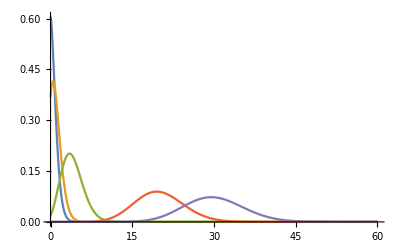

```mathematica
Plot[Table[prob[λ,k],{λ,{0.5, 1, 4, 20, 30}}]//Evaluate,{k,0, 60},PlotRange->All]
```

```mathematica
iprob[λ_, k_]=-Integrate[prob[λ,k],λ]
```

0.606531 ⅇ^k (0.5+k)^(-0.5-k) Gamma[1+k,λ]

```mathematica
Solve[iprob[λ,k],λ]
```

Solve::naqs: 0.606531 ⅇ^k (0.5+k)^(-0.5-k) Gamma[1+k,λ] is not a quantified system of equations and inequalities.

Solve[0.606531 ⅇ^k (0.5+k)^(-0.5-k) Gamma[1+k,λ],λ]

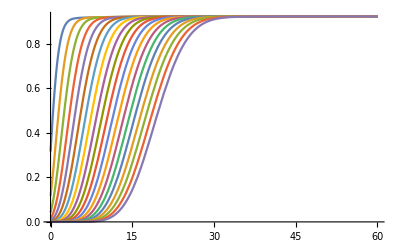

```mathematica
Plot[Table[iprob[λ,k],{λ,1,20}]//Evaluate,{k,0, 60},PlotRange->All]
```

```mathematica
cumprob[λ_, k_]=Gamma[1+k,λ]/Gamma[1+k]
```

Gamma[1+k,λ]/Gamma[1+k]

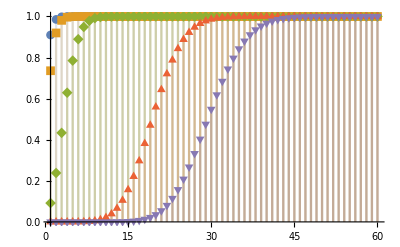

```mathematica
DiscretePlot[Table[cumprob[λ,k],{λ,{0.5, 1, 4, 20, 30}}]//Evaluate,{k,1, 60},PlotRange->All, PlotMarkers->Automatic]
```

```mathematica
normprob[λ_, k_,q_]=(cumprob[λ, k] - cumprob[λ, Max[0,k-q]])/(cumprob[λ, k+q] - cumprob[λ, Max[0,k-q]])
```

(Gamma[1+k,λ]/Gamma[1+k]-Gamma[1+Max[0,k-q],λ]/Gamma[1+Max[0,k-q]])/(Gamma[1+k+q,λ]/Gamma[1+k+q]-Gamma[1+Max[0,k-q],λ]/Gamma[1+Max[0,k-q]])

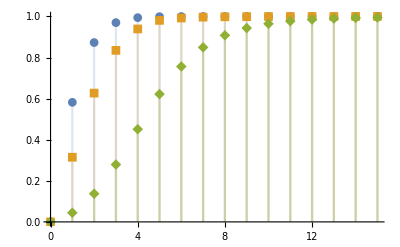

```mathematica
DiscretePlot[Table[normprob[λ,k,5],{λ,{1, 2, 5}}]//Evaluate,{k,0, 15},PlotRange->All, PlotMarkers->Automatic]
```

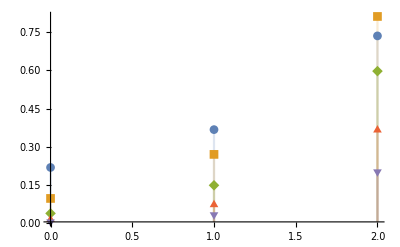

```mathematica
DiscretePlot[Table[Gamma[k,λ]*(λ),{λ,1,5}]//Evaluate,{k,0, 2},PlotRange->All, PlotMarkers->Automatic]
```

```mathematica
((i-1)*(1-t)+i*t)/n
```

((-1+i) (1-t)+i t)/n